```mathematica
(* Predictive Taxonomy *)
(* Roger Sessions: “If you’re sorting e Elements into s Sets of a partition,then how many of e do you need to run through the partitioning algorithm before you’ve identified most of the sets that will eventually make P?”

This notebook addresses the harder problem: If you don't know how many distinct elements (i.e. categories) you have, can you still predict the number of elements (within a reasonable range) after a given number of observations?

catsUncovered is the main function. For a given number of categories and a given number of observations, how many categories would you expect to observe? What percentage of the categories does this constitute? The function simulates a number of trials and takes the mean value of the categories uncovered as the answer. It also produces all the usual statistics on the trials -- stddev, quartiles, etc. Each set of trials is set to be nRequirements long. The idea is that the total number of requirements will be some largish number, say 1,000. Within these requirements, the categories will be scattered randomly.
 *)
```

```mathematica
catsUncovered[nCategories_, nObservations_]:= Module[{nRequirements = 1000, 
nTrials = 50,
seedRandomFlag = 0,
series, 
obs, 
nCatsNotFound, 
nCatsFound, 
percentCatsFound,
percentStats,
numStats,
mean, stddev, quartiles, iqrange, min, max },
(* Output is the 2-tuple of statistics for the mean percentage of categories uncovered and the mean number of categories uncovered *)
(* generate the series nTrials times -- categories randomly occurring in nRequirements *)
(* Set SeedRandom to make sure that the same series is used in all trials -- i.e. there is essentialy only 1 trial *)
If[seedRandomFlag == 1,SeedRandom[1]];
series = Table[RandomInteger[{1, nCategories}, nRequirements], {nTrials}];
(* Take the first nObservations for each trial *)
obs = Take[#, nObservations] & /@ series;
(* Find the number of categories that are NOT present in the obs *)
nCatsNotFound = Length[Complement[Range[nCategories], #]] & /@ obs;
(* The number of categories found is total categories minus categories not found *)
nCatsFound = nCategories - # & /@ nCatsNotFound;
(* Percentage of categories found to total number of categories *)
percentCatsFound = N[#/nCategories] & /@ nCatsFound;
(* percentCatsFound statistics for the trials *)
percentStats = {mean, stddev, quartiles, iqrange, min, max} = #[percentCatsFound] & /@ {Mean, StandardDeviation, Quartiles, InterquartileRange, Min, Max};
(* number of categories found statistics for the trials *)
numStats = {mean, stddev, quartiles, iqrange, min, max} = N[#[nCatsFound]] & /@ {Mean, StandardDeviation, Quartiles, InterquartileRange, Min, Max};
{percentStats, numStats}
];
```

```mathematica
(* Percentage and number of categories uncovered in n observations (second argument)if there are a total of c categories (first argument) *)
catsUncovered[20, 20]
```

{{0.632,0.0793854,{0.6,0.625,0.7},0.1,0.45,0.8},{12.64,1.58771,{12.,12.5,14.},2.,9.,16.}}

```mathematica
(* Get data for tables and graphs -- nCategories go from 20, 40, ..., 100 and nObservations go from 1 to 200. For each data point, the mean percentage categories uncovered and the mean number of categories uncovered is output *)
t = Table[Flatten[{i, j, catsUncovered[i,j] }],{i, 20, 100, 10}, {j, 1, 200}];
```

```mathematica
(* Pull just the category, observations, mean percentage uncovered, and the mean number uncovered *)
t1 = Table[{t[[i]][[j]][[1]], t[[i]][[j]][[2]], t[[i]][[j]][[3]], t[[i]][[j]][[11]]}, {i, 1,9}, {j, 1, 200}];
```

```mathematica
(* Pull the mean number uncovered *)
d1 = #[[All, 4]] & /@ t1;
```

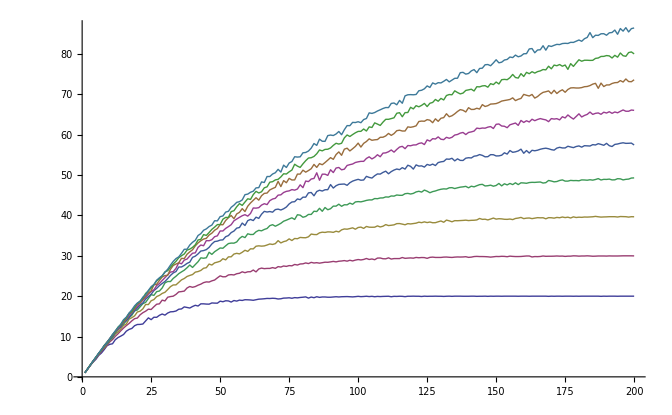

```mathematica
g1 = ListLinePlot[d1, PlotRange->{All, All}]
```

```mathematica
(* Pull the mean percentage uncovered *)
d2 = #[[All, 3]] & /@ t1;
```

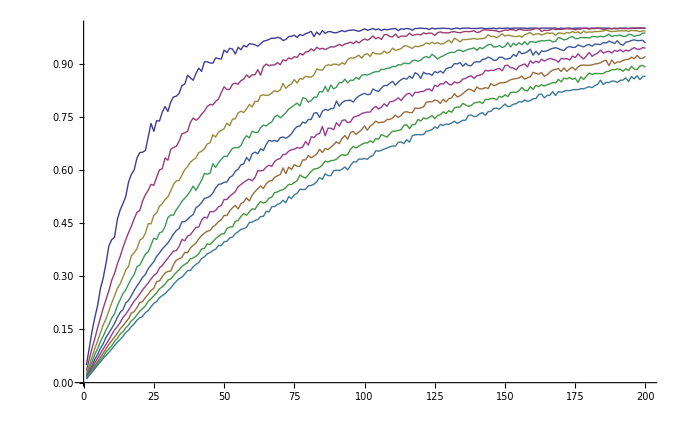

```mathematica
g2 = ListLinePlot[d2, PlotRange->{All, All}]
```

```mathematica
(* Data in tabular form *)
```

```mathematica
(* Number of categories uncovered for 20, ..., 100 categories and 1, 2, ..., 200 observations. *)
t2 = Table[Floor[#] & /@ t[[i]][[All, 11]], {i, 1,9}]ᵀ;
```

```mathematica
(* Add the number of observations number to each element in t2 *)
(* Create a function for doing this *)
t3 = Table[Prepend[t2[[i]], i], {i, 1, Length[t2]}];
```

```mathematica
(* Add the column headings *)
t4= Prepend[t3, {"Number of\nObservations", "20\nCategories", "30\nCategories", "40\nCategories", "50\nCategories", "60\nCategories", "70\nCategories", "80\nCategories", "90\nCategories", "100\nCategories"}];
```

```mathematica
(* Each cell in this table shows the number of categories uncovered given the number of observations made (left-most column) and the number of categories present (top-most row). For example, if there are 20 observations made and there are 50 categories, then we should expect to see roughly 16 of those 50 categories observed. *)
```

```mathematica
t5 = Grid[t4, Dividers->All]
```

Number of
Observations | 20
Categories | 30
Categories | 40
Categories | 50
Categories | 60
Categories | 70
Categories | 80
Categories | 90
Categories | 100
Categories
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2
3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
4 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 3
5 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
6 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5
7 | 5 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
8 | 6 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
9 | 7 | 7 | 8 | 8 | 8 | 8 | 8 | 8 | 8
10 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9 | 9
11 | 8 | 9 | 9 | 9 | 10 | 10 | 10 | 10 | 10
12 | 9 | 10 | 10 | 10 | 11 | 11 | 11 | 11 | 11
13 | 9 | 10 | 11 | 11 | 11 | 11 | 12 | 12 | 12
14 | 10 | 11 | 11 | 12 | 12 | 12 | 12 | 12 | 13
15 | 10 | 12 | 12 | 13 | 13 | 13 | 13 | 13 | 14
16 | 11 | 12 | 13 | 13 | 13 | 14 | 14 | 14 | 14
17 | 11 | 13 | 14 | 14 | 14 | 15 | 15 | 15 | 15
18 | 12 | 13 | 14 | 15 | 15 | 16 | 16 | 16 | 16
19 | 12 | 14 | 15 | 16 | 16 | 16 | 16 | 17 | 17
20 | 12 | 14 | 16 | 16 | 17 | 17 | 18 | 18 | 18
21 | 13 | 15 | 16 | 17 | 17 | 18 | 18 | 18 | 18
22 | 13 | 15 | 16 | 18 | 18 | 19 | 19 | 19 | 19
23 | 13 | 16 | 17 | 18 | 19 | 19 | 19 | 20 | 20
24 | 14 | 16 | 17 | 19 | 19 | 20 | 20 | 21 | 21
25 | 14 | 16 | 18 | 20 | 20 | 21 | 21 | 22 | 22
26 | 14 | 17 | 19 | 20 | 21 | 21 | 22 | 22 | 22
27 | 14 | 18 | 19 | 21 | 21 | 22 | 22 | 23 | 23
28 | 15 | 18 | 20 | 21 | 22 | 23 | 23 | 24 | 24
29 | 15 | 19 | 20 | 22 | 23 | 23 | 24 | 25 | 25
30 | 15 | 18 | 20 | 23 | 23 | 24 | 25 | 26 | 25
31 | 15 | 19 | 21 | 23 | 24 | 25 | 25 | 26 | 26
32 | 16 | 19 | 22 | 23 | 25 | 25 | 26 | 27 | 27
33 | 16 | 20 | 22 | 24 | 25 | 26 | 27 | 27 | 28
34 | 16 | 20 | 22 | 24 | 26 | 26 | 27 | 28 | 29
35 | 16 | 21 | 23 | 25 | 27 | 28 | 28 | 29 | 29
36 | 16 | 21 | 24 | 26 | 27 | 28 | 29 | 30 | 30
37 | 17 | 21 | 24 | 26 | 27 | 28 | 29 | 30 | 31
38 | 17 | 22 | 24 | 27 | 28 | 29 | 30 | 31 | 31
39 | 17 | 22 | 25 | 27 | 28 | 29 | 30 | 31 | 32
40 | 17 | 22 | 25 | 27 | 29 | 30 | 31 | 32 | 33
41 | 17 | 22 | 25 | 27 | 29 | 30 | 32 | 32 | 33
42 | 17 | 22 | 26 | 28 | 30 | 32 | 33 | 33 | 35
43 | 18 | 22 | 26 | 29 | 31 | 32 | 33 | 34 | 35
44 | 18 | 23 | 26 | 29 | 31 | 32 | 34 | 35 | 36
45 | 18 | 23 | 27 | 29 | 31 | 33 | 34 | 35 | 36
46 | 18 | 23 | 27 | 30 | 32 | 33 | 35 | 35 | 37
47 | 18 | 23 | 27 | 30 | 32 | 34 | 35 | 36 | 37
48 | 18 | 24 | 28 | 31 | 33 | 34 | 36 | 37 | 38
49 | 18 | 24 | 28 | 31 | 33 | 34 | 36 | 37 | 38
50 | 18 | 25 | 28 | 31 | 33 | 36 | 37 | 37 | 39
51 | 18 | 24 | 29 | 31 | 33 | 36 | 37 | 39 | 39
52 | 18 | 24 | 29 | 32 | 34 | 36 | 38 | 39 | 40
53 | 18 | 25 | 29 | 33 | 35 | 37 | 39 | 39 | 41
54 | 18 | 25 | 29 | 33 | 35 | 37 | 40 | 40 | 42
55 | 18 | 25 | 30 | 33 | 36 | 38 | 39 | 41 | 42
56 | 18 | 25 | 30 | 33 | 36 | 39 | 40 | 42 | 43
57 | 19 | 25 | 30 | 34 | 37 | 39 | 40 | 42 | 43
58 | 18 | 26 | 30 | 34 | 38 | 39 | 41 | 42 | 43
59 | 19 | 25 | 31 | 34 | 37 | 40 | 40 | 43 | 45
60 | 19 | 26 | 31 | 35 | 38 | 39 | 42 | 44 | 45
61 | 19 | 26 | 31 | 35 | 39 | 40 | 43 | 43 | 45
62 | 18 | 26 | 31 | 35 | 38 | 41 | 43 | 45 | 46
63 | 19 | 26 | 32 | 35 | 39 | 41 | 44 | 45 | 46
64 | 19 | 26 | 32 | 36 | 39 | 41 | 43 | 45 | 46
65 | 19 | 26 | 32 | 36 | 40 | 42 | 44 | 45 | 48
66 | 19 | 26 | 32 | 36 | 41 | 42 | 45 | 46 | 48
67 | 19 | 26 | 32 | 36 | 40 | 42 | 45 | 47 | 49
68 | 19 | 26 | 32 | 37 | 40 | 43 | 46 | 48 | 49
69 | 19 | 27 | 32 | 37 | 40 | 44 | 46 | 48 | 50
70 | 19 | 26 | 33 | 37 | 41 | 44 | 46 | 48 | 50
71 | 19 | 27 | 33 | 37 | 41 | 45 | 48 | 48 | 51
72 | 19 | 27 | 33 | 38 | 41 | 45 | 47 | 49 | 50
73 | 19 | 27 | 33 | 38 | 41 | 45 | 48 | 50 | 52
74 | 19 | 27 | 33 | 38 | 42 | 45 | 48 | 50 | 51
75 | 19 | 27 | 34 | 39 | 42 | 46 | 49 | 50 | 53
76 | 19 | 27 | 33 | 39 | 43 | 46 | 48 | 51 | 53
77 | 19 | 27 | 34 | 39 | 43 | 46 | 48 | 52 | 54
78 | 19 | 27 | 34 | 40 | 44 | 46 | 50 | 52 | 54
79 | 19 | 27 | 34 | 40 | 43 | 47 | 50 | 51 | 54
80 | 19 | 28 | 34 | 39 | 44 | 46 | 51 | 52 | 55
81 | 19 | 28 | 34 | 39 | 44 | 48 | 50 | 53 | 55
82 | 19 | 28 | 34 | 40 | 45 | 48 | 51 | 54 | 55
83 | 19 | 28 | 35 | 40 | 45 | 49 | 51 | 54 | 56
84 | 19 | 28 | 35 | 41 | 44 | 49 | 52 | 54 | 57
85 | 19 | 28 | 35 | 40 | 45 | 50 | 51 | 55 | 57
86 | 19 | 28 | 35 | 41 | 46 | 48 | 52 | 56 | 58
87 | 19 | 28 | 35 | 41 | 46 | 50 | 52 | 56 | 58
88 | 19 | 28 | 35 | 41 | 46 | 50 | 53 | 56 | 58
89 | 19 | 28 | 35 | 41 | 46 | 49 | 53 | 56 | 59
90 | 19 | 28 | 35 | 41 | 47 | 51 | 54 | 56 | 59
91 | 19 | 28 | 35 | 42 | 46 | 50 | 53 | 57 | 59
92 | 19 | 28 | 36 | 42 | 47 | 51 | 55 | 57 | 60
93 | 19 | 28 | 35 | 42 | 47 | 51 | 55 | 57 | 60
94 | 19 | 28 | 36 | 42 | 47 | 51 | 54 | 57 | 60
95 | 19 | 28 | 36 | 42 | 47 | 51 | 56 | 59 | 61
96 | 19 | 28 | 36 | 42 | 47 | 52 | 56 | 59 | 62
97 | 19 | 28 | 36 | 43 | 48 | 52 | 56 | 59 | 62
98 | 19 | 28 | 36 | 42 | 48 | 52 | 56 | 60 | 63
99 | 19 | 28 | 36 | 43 | 48 | 53 | 57 | 60 | 63
100 | 19 | 29 | 37 | 43 | 48 | 53 | 57 | 60 | 63
101 | 19 | 28 | 37 | 43 | 48 | 53 | 56 | 60 | 63
102 | 19 | 29 | 36 | 43 | 48 | 53 | 57 | 61 | 63
103 | 19 | 29 | 37 | 43 | 49 | 54 | 58 | 60 | 64
104 | 19 | 29 | 37 | 43 | 49 | 54 | 59 | 61 | 65
105 | 19 | 29 | 37 | 43 | 49 | 54 | 58 | 61 | 65
106 | 19 | 29 | 37 | 44 | 49 | 54 | 58 | 62 | 65
107 | 19 | 29 | 37 | 44 | 50 | 55 | 58 | 62 | 65
108 | 19 | 29 | 37 | 44 | 50 | 54 | 59 | 62 | 66
109 | 19 | 29 | 37 | 44 | 50 | 55 | 59 | 63 | 66
110 | 19 | 29 | 37 | 44 | 50 | 55 | 59 | 63 | 66
111 | 19 | 29 | 37 | 44 | 50 | 55 | 60 | 63 | 66
112 | 19 | 29 | 37 | 44 | 50 | 56 | 59 | 64 | 67
113 | 19 | 29 | 37 | 44 | 51 | 55 | 60 | 64 | 67
114 | 19 | 29 | 37 | 45 | 51 | 56 | 61 | 65 | 67
115 | 19 | 29 | 38 | 45 | 51 | 56 | 61 | 65 | 68
116 | 19 | 29 | 37 | 45 | 51 | 57 | 60 | 64 | 67
117 | 19 | 29 | 37 | 45 | 51 | 56 | 60 | 65 | 69
118 | 19 | 29 | 37 | 45 | 52 | 57 | 61 | 65 | 69
119 | 19 | 29 | 37 | 45 | 52 | 57 | 61 | 66 | 69
120 | 20 | 29 | 38 | 45 | 51 | 57 | 62 | 66 | 69
121 | 19 | 29 | 38 | 45 | 52 | 57 | 62 | 67 | 70
122 | 19 | 29 | 38 | 46 | 52 | 57 | 63 | 66 | 70
123 | 19 | 29 | 38 | 45 | 52 | 58 | 63 | 67 | 71
124 | 20 | 29 | 38 | 46 | 52 | 57 | 63 | 67 | 71
125 | 19 | 29 | 38 | 46 | 52 | 58 | 63 | 67 | 72
126 | 19 | 29 | 38 | 45 | 52 | 58 | 63 | 67 | 71
127 | 19 | 29 | 38 | 45 | 52 | 59 | 63 | 68 | 72
128 | 20 | 29 | 38 | 46 | 52 | 58 | 63 | 68 | 72
129 | 19 | 29 | 38 | 46 | 53 | 59 | 63 | 68 | 72
130 | 19 | 29 | 38 | 46 | 53 | 58 | 64 | 69 | 72
131 | 19 | 29 | 38 | 46 | 53 | 58 | 64 | 68 | 73
132 | 19 | 29 | 38 | 46 | 54 | 59 | 65 | 69 | 73
133 | 20 | 29 | 38 | 46 | 53 | 59 | 64 | 69 | 73
134 | 19 | 29 | 38 | 46 | 54 | 59 | 64 | 69 | 73
135 | 20 | 29 | 38 | 46 | 53 | 59 | 65 | 70 | 74
136 | 20 | 29 | 38 | 46 | 54 | 60 | 65 | 70 | 74
137 | 20 | 29 | 38 | 47 | 53 | 60 | 66 | 70 | 75
138 | 19 | 29 | 38 | 47 | 53 | 60 | 66 | 70 | 75
139 | 19 | 29 | 38 | 47 | 54 | 60 | 65 | 71 | 75
140 | 19 | 29 | 38 | 46 | 54 | 60 | 66 | 71 | 75
141 | 20 | 29 | 38 | 47 | 54 | 60 | 66 | 71 | 75
142 | 20 | 29 | 38 | 47 | 54 | 60 | 66 | 70 | 76
143 | 19 | 29 | 38 | 47 | 54 | 61 | 66 | 71 | 75
144 | 19 | 29 | 39 | 47 | 55 | 61 | 66 | 71 | 76
145 | 19 | 29 | 39 | 47 | 54 | 61 | 67 | 72 | 76
146 | 20 | 29 | 39 | 47 | 54 | 61 | 67 | 72 | 77
147 | 19 | 29 | 38 | 47 | 54 | 61 | 67 | 71 | 77
148 | 20 | 29 | 39 | 47 | 55 | 62 | 67 | 72 | 77
149 | 19 | 29 | 39 | 47 | 55 | 61 | 67 | 72 | 77
150 | 20 | 29 | 39 | 47 | 54 | 62 | 67 | 73 | 78
151 | 20 | 29 | 39 | 47 | 54 | 62 | 68 | 72 | 77
152 | 19 | 29 | 39 | 47 | 54 | 62 | 68 | 73 | 78
153 | 20 | 29 | 39 | 47 | 55 | 62 | 68 | 73 | 78
154 | 20 | 29 | 39 | 47 | 55 | 61 | 68 | 73 | 78
155 | 20 | 29 | 39 | 47 | 56 | 62 | 68 | 74 | 79
156 | 20 | 29 | 38 | 47 | 55 | 62 | 69 | 74 | 79
157 | 20 | 29 | 39 | 48 | 55 | 62 | 68 | 74 | 79
158 | 19 | 29 | 39 | 47 | 56 | 62 | 68 | 74 | 79
159 | 20 | 29 | 39 | 48 | 56 | 63 | 69 | 75 | 79
160 | 20 | 29 | 39 | 48 | 55 | 63 | 70 | 74 | 80
161 | 20 | 29 | 39 | 47 | 56 | 63 | 69 | 75 | 80
162 | 19 | 29 | 39 | 48 | 55 | 63 | 69 | 75 | 81
163 | 20 | 29 | 39 | 48 | 56 | 63 | 70 | 75 | 81
164 | 20 | 29 | 39 | 48 | 56 | 63 | 69 | 75 | 80
165 | 20 | 29 | 39 | 48 | 56 | 63 | 69 | 75 | 81
166 | 20 | 29 | 39 | 48 | 56 | 64 | 70 | 75 | 81
167 | 20 | 29 | 39 | 48 | 56 | 63 | 70 | 76 | 82
168 | 20 | 29 | 39 | 48 | 56 | 63 | 70 | 76 | 80
169 | 19 | 29 | 39 | 48 | 56 | 63 | 70 | 77 | 82
170 | 20 | 29 | 39 | 48 | 56 | 64 | 70 | 76 | 81
171 | 19 | 29 | 39 | 48 | 56 | 63 | 71 | 77 | 82
172 | 20 | 29 | 39 | 48 | 56 | 64 | 70 | 77 | 82
173 | 20 | 29 | 39 | 48 | 56 | 63 | 70 | 77 | 82
174 | 19 | 29 | 39 | 48 | 56 | 64 | 71 | 77 | 82
175 | 20 | 29 | 39 | 48 | 56 | 64 | 70 | 77 | 82
176 | 20 | 29 | 39 | 48 | 57 | 64 | 71 | 76 | 82
177 | 20 | 29 | 39 | 48 | 56 | 64 | 71 | 77 | 82
178 | 19 | 30 | 39 | 48 | 56 | 63 | 71 | 76 | 82
179 | 20 | 29 | 39 | 48 | 57 | 64 | 71 | 77 | 83
180 | 19 | 29 | 39 | 48 | 57 | 65 | 71 | 78 | 83
181 | 20 | 29 | 39 | 48 | 56 | 64 | 71 | 78 | 83
182 | 20 | 29 | 39 | 48 | 57 | 64 | 71 | 78 | 83
183 | 20 | 30 | 39 | 48 | 57 | 65 | 71 | 78 | 84
184 | 20 | 29 | 39 | 48 | 57 | 65 | 72 | 78 | 85
185 | 20 | 29 | 39 | 48 | 57 | 65 | 72 | 78 | 84
186 | 20 | 29 | 39 | 48 | 57 | 65 | 72 | 78 | 84
187 | 20 | 29 | 39 | 49 | 57 | 65 | 71 | 79 | 84
188 | 19 | 29 | 39 | 48 | 57 | 65 | 72 | 79 | 85
189 | 20 | 29 | 39 | 48 | 57 | 65 | 71 | 79 | 85
190 | 19 | 29 | 39 | 48 | 57 | 65 | 72 | 79 | 84
191 | 20 | 29 | 39 | 49 | 57 | 65 | 72 | 79 | 85
192 | 20 | 29 | 39 | 48 | 57 | 65 | 72 | 79 | 85
193 | 20 | 29 | 39 | 48 | 57 | 65 | 72 | 79 | 85
194 | 19 | 29 | 39 | 49 | 57 | 65 | 72 | 79 | 84
195 | 20 | 29 | 39 | 49 | 57 | 65 | 73 | 80 | 86
196 | 20 | 30 | 39 | 48 | 58 | 66 | 73 | 79 | 85
197 | 20 | 30 | 39 | 48 | 57 | 65 | 73 | 79 | 86
198 | 20 | 30 | 39 | 49 | 57 | 65 | 73 | 80 | 85
199 | 20 | 30 | 39 | 49 | 57 | 66 | 73 | 80 | 86
200 | 20 | 29 | 39 | 49 | 57 | 66 | 73 | 80 | 86

```mathematica
(* Let's investigate the claim that synergy-driven partitions result in minimal complexity *)
(* Sessions,page 22:"Synergy:Two business functions have synergy with each other if and only if from the business perspective neither is useful without the other." *)
```

```mathematica
(* Sessions, MathOfITSimplification-103.pdf,p.29:"Recall that most of the SIP activity occurs in the partitioning phase,or what I often call the preplanning phase.The main goal of this phase is to identify the basic structure of the project partition.To do this we generate a representative selection of business functions,say 10% of the expected total.We then use synergy analysis on that selection to drive the partition.This partition will define the structure and packaging of the technical solution.

Since synergy is an equivalence relation,the partition that is created is unique and can be validated.Because the methodology is deterministic,there is only one way it can turn out regardless of who isdriving theprocess and  what random selection of business functions happen to be picked for the analysis.The partition generated will be the simplest possible,because synergy limits the number of business functions that will live together.Only those with synergy are allowed to cohabitate.And it also limits the coordination complexity by grouping together those with the most likely dependencies.The fact that we can limit the coordination dependencies without knowing what those dependencies are is part of what appears to be magic.Remember all partitions generated with equivalence relations have the property of conservation of structure.This guarantees that the partition we identified with the small group of business functions will not change as we discover more business functions.This is important because upwards of 90% of the business functions and all of their dependencies are still unknown during the partitioning phase.They won’t be discovered until the design phase or even later." *)

(* Partitions satisfy the following conditions: (1) can't contain the empty set, (2) Pairwise disjoint (intersection must be empty), (3) Union must be the orginial set. *)
```

```mathematica
Clear[c]
```

```mathematica
s = {a,b,c}
```

{a,b,c}

```mathematica
s1 = Tuples[s, 1]
```

{{a},{b},{c}}

```mathematica
(* Definitely know that s1 is a partition. Will add it on to the rest of the partitions at the end *)
```

```mathematica
s2 = Tuples[s,2]
```

{{a,a},{a,b},{a,c},{b,a},{b,b},{b,c},{c,a},{c,b},{c,c}}

```mathematica
(* Set of all subsets of s with the empty set removed *)
```

```mathematica
ss = Select[Subsets[s], Length[#] > 0 &]
```

{{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}}

```mathematica
ss2 = Tuples[ss, 2];
```

```mathematica
ss3 = Tuples[ss, 3];
```

```mathematica
(* Apply the conditions for the partition *)
ss2p =  Select[ss2, (Length[#[[1]] ∩ #[[2]]] == 0) && (Sort[#[[1]] ∪ #[[2]]]== Sort[s])&]
```

{{{a},{b,c}},{{b},{a,c}},{{c},{a,b}},{{a,b},{c}},{{a,c},{b}},{{b,c},{a}}}

```mathematica
(* Apply the conditions for the partition *)
ss3p =  Select[ss3, (Length[#[[1]] ∩ #[[2]] ∩ #[[3]]] == 0) && (Sort[#[[1]] ∪ #[[2]] ∪ #[[3]]]== Sort[s])&]
```

{{{a},{a},{b,c}},{{a},{b},{c}},{{a},{b},{a,c}},{{a},{b},{b,c}},{{a},{b},{a,b,c}},{{a},{c},{b}},{{a},{c},{a,b}},{{a},{c},{b,c}},{{a},{c},{a,b,c}},{{a},{a,b},{c}},{{a},{a,b},{b,c}},{{a},{a,c},{b}},{{a},{a,c},{b,c}},{{a},{b,c},{a}},{{a},{b,c},{b}},{{a},{b,c},{c}},{{a},{b,c},{a,b}},{{a},{b,c},{a,c}},{{a},{b,c},{b,c}},{{a},{b,c},{a,b,c}},{{a},{a,b,c},{b}},{{a},{a,b,c},{c}},{{a},{a,b,c},{b,c}},{{b},{a},{c}},{{b},{a},{a,c}},{{b},{a},{b,c}},{{b},{a},{a,b,c}},{{b},{b},{a,c}},{{b},{c},{a}},{{b},{c},{a,b}},{{b},{c},{a,c}},{{b},{c},{a,b,c}},{{b},{a,b},{c}},{{b},{a,b},{a,c}},{{b},{a,c},{a}},{{b},{a,c},{b}},{{b},{a,c},{c}},{{b},{a,c},{a,b}},{{b},{a,c},{a,c}},{{b},{a,c},{b,c}},{{b},{a,c},{a,b,c}},{{b},{b,c},{a}},{{b},{b,c},{a,c}},{{b},{a,b,c},{a}},{{b},{a,b,c},{c}},{{b},{a,b,c},{a,c}},{{c},{a},{b}},{{c},{a},{a,b}},{{c},{a},{b,c}},{{c},{a},{a,b,c}},{{c},{b},{a}},{{c},{b},{a,b}},{{c},{b},{a,c}},{{c},{b},{a,b,c}},{{c},{c},{a,b}},{{c},{a,b},{a}},{{c},{a,b},{b}},{{c},{a,b},{c}},{{c},{a,b},{a,b}},{{c},{a,b},{a,c}},{{c},{a,b},{b,c}},{{c},{a,b},{a,b,c}},{{c},{a,c},{b}},{{c},{a,c},{a,b}},{{c},{b,c},{a}},{{c},{b,c},{a,b}},{{c},{a,b,c},{a}},{{c},{a,b,c},{b}},{{c},{a,b,c},{a,b}},{{a,b},{a},{c}},{{a,b},{a},{b,c}},{{a,b},{b},{c}},{{a,b},{b},{a,c}},{{a,b},{c},{a}},{{a,b},{c},{b}},{{a,b},{c},{c}},{{a,b},{c},{a,b}},{{a,b},{c},{a,c}},{{a,b},{c},{b,c}},{{a,b},{c},{a,b,c}},{{a,b},{a,b},{c}},{{a,b},{a,c},{b}},{{a,b},{a,c},{c}},{{a,b},{a,c},{b,c}},{{a,b},{b,c},{a}},{{a,b},{b,c},{c}},{{a,b},{b,c},{a,c}},{{a,b},{a,b,c},{c}},{{a,c},{a},{b}},{{a,c},{a},{b,c}},{{a,c},{b},{a}},{{a,c},{b},{b}},{{a,c},{b},{c}},{{a,c},{b},{a,b}},{{a,c},{b},{a,c}},{{a,c},{b},{b,c}},{{a,c},{b},{a,b,c}},{{a,c},{c},{b}},{{a,c},{c},{a,b}},{{a,c},{a,b},{b}},{{a,c},{a,b},{c}},{{a,c},{a,b},{b,c}},{{a,c},{a,c},{b}},{{a,c},{b,c},{a}},{{a,c},{b,c},{b}},{{a,c},{b,c},{a,b}},{{a,c},{a,b,c},{b}},{{b,c},{a},{a}},{{b,c},{a},{b}},{{b,c},{a},{c}},{{b,c},{a},{a,b}},{{b,c},{a},{a,c}},{{b,c},{a},{b,c}},{{b,c},{a},{a,b,c}},{{b,c},{b},{a}},{{b,c},{b},{a,c}},{{b,c},{c},{a}},{{b,c},{c},{a,b}},{{b,c},{a,b},{a}},{{b,c},{a,b},{c}},{{b,c},{a,b},{a,c}},{{b,c},{a,c},{a}},{{b,c},{a,c},{b}},{{b,c},{a,c},{a,b}},{{b,c},{b,c},{a}},{{b,c},{a,b,c},{a}},{{a,b,c},{a},{b}},{{a,b,c},{a},{c}},{{a,b,c},{a},{b,c}},{{a,b,c},{b},{a}},{{a,b,c},{b},{c}},{{a,b,c},{b},{a,c}},{{a,b,c},{c},{a}},{{a,b,c},{c},{b}},{{a,b,c},{c},{a,b}},{{a,b,c},{a,b},{c}},{{a,b,c},{a,c},{b}},{{a,b,c},{b,c},{a}}}